## Section | Conic Sections

Conic sections have the form of a second-degree polynomial:

a x^2+b x y+c y^2+d x+e y+f==0

A curve passing through five points {x_i,y_i}_(i=1,…5) can be computed by solving the following determinantal equation:

|x^2 | x y | y^2 | x | y | 1
x_1^2 | x_1 y_1 | y_1^2 | x_1 | y_1 | 1
x_2^2 | x_2 y_2 | y_2^2 | x_2 | y_2 | 1
x_3^2 | x_3 y_3 | y_3^2 | x_3 | y_3 | 1
x_4^2 | x_4 y_4 | y_4^2 | x_4 | y_4 | 1
x_5^2 | x_5 y_5 | y_5^2 | x_5 | y_5 | 1|==0

Use the determinantal equation (DisplayFormulaNumbered) to compute the equation of the curve passing through 5 randomly chosen points, computed using RandomReal. [3 Marks]

Use ContourPlot to visualize the curve. Show the curve together with the points. [2 Marks]

### Solution

Each row of the matrix can be constucted from a point {x,y} using a function:

```mathematica
makeRow[{x_,y_}]:={x^2,x y,y^2,x,y,1}
```

Compute the equation of the curve by constructing the matrix and computing the determinant:

```mathematica
conic[x_,y_][pts_]:=Det[makeRow/@Join[{{x,y}},pts]]
```

Check that it works on a random set of points:

```mathematica
pts=RandomReal[{-1,1},{5,2}]
```

(-0.622088 | -0.057854
0.945733 | -0.454633
0.40561 | -0.529854
0.373552 | 0.627669
0.131531 | -0.55893)

```mathematica
conic[x,y][pts]
```

0.0102745 x^2-0.0598044 x y-0.0282633 x+0.0835087 y^2+0.0144882 y-0.0188473

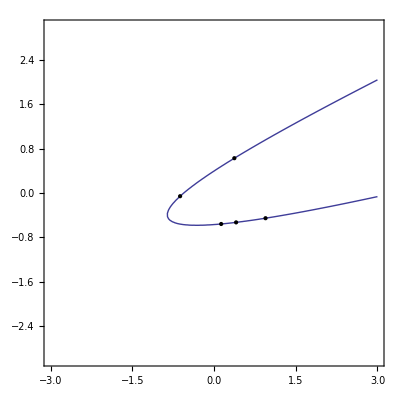

```mathematica
Show[ContourPlot[%==0,{x,-3,3},{y,-3,3},PlotPoints->50],Graphics[Point[pts]]]
```

Make this dynamic:

```mathematica
Manipulate[
ContourPlot[conic[x,y][r]==0,{x,-3,3},{y,-3,3},PlotPoints->50],
{{r,RandomReal[{-1,1},{5,2}]},{-3,-3},{3,3},Locator},SaveDefinitions-> True]
```